```mathematica
(* case k=0 *)
r0=1/10;
ϵ=1/10^10000;
L=100; 
ρ=(2Pi)/L;
```

```mathematica
CC=r0;
Print["Constant C = ",CC];
```

Constant C = 1/10

```mathematica
q[τ_]:=-(Sin[τ]^(n-1)Cos[τ]^(n-1))/(Sin[τ]^(2n)+Cos[τ]^(2n))
p[τ_]:=(Sin[τ]^(2n-1)Cos[τ]-Cos[τ]^(2n-1)Sin[τ])/(Sin[τ]^(2n)+Cos[τ]^(2n))
II[ϕ_]:=-∫_0^ϕ q[τ]ⅆτ
(*K=II[2Pi]/(2Pi);*)
K=1/n;
R[ϕ_]:=∫_0^ϕ (p[τ]-q[τ])ⅆτ - K ϕ;
```

```mathematica
II2[τ_]=FullSimplify[∫(p[τ]-q[τ])ⅆτ];
FunII2[τ_]:=Module[{res},
If[τ<0||τ>2Pi,Abort[]];
If[τ≤Pi/2,res=Limit[II2[t],t->τ,Direction->"FromBelow"]-Limit[II2[t],t->0,Direction->"FromAbove"];,
If[τ≤3Pi/2,res=(Limit[II2[t],t->Pi/2,Direction->"FromBelow"]-Limit[II2[t],t->0,Direction->"FromAbove"])+(Limit[II2[t],t->τ,Direction->"FromBelow"]-Limit[II2[t],t->Pi/2,Direction->"FromAbove"]);,
res=(Limit[II2[t],t->Pi/2,Direction->"FromBelow"]-Limit[II2[t],t->0,Direction->"FromAbove"])+(Limit[II2[t],t->3Pi/2,Direction->"FromBelow"]-Limit[II2[t],t->Pi/2,Direction->"FromAbove"])+
(Limit[II2[t],t->τ,Direction->"FromBelow"]-Limit[II2[t],t->3Pi/2,Direction->"FromAbove"]);
];
];
res
]
```

```mathematica
Print[II2[τ]];
```

-(((2 ArcTan[(Sec[τ]^2)^(n/2) (Tan[τ]/(√(Sec[τ]^2)))^n]-n Log[Sec[τ]^2]+Log[1+(Sec[τ]^2)^n (Tan[τ]/(√(Sec[τ]^2)))^(2 n)]) (Cos[τ]^(2 n) Sin[τ]^2-Cos[τ]^n Sin[τ]^n-Cos[τ]^2 Sin[τ]^(2 n)) (1+(Sec[τ]^2)^n (Tan[τ]/(√(Sec[τ]^2)))^(2 n)))/(2 n (Cos[τ]^(2 n)+Sin[τ]^(2 n)) (-Sin[τ]^2+(Sec[τ]^2)^(n/2) (Tan[τ]/(√(Sec[τ]^2)))^n+(Sec[τ]^2)^(-1+n) (Tan[τ]/(√(Sec[τ]^2)))^(2 n))))

```mathematica
n=21;
Print["Constant K = ",K];
Print[II2[τ]];
```

Constant K = 1/21

-(((2 ArcTan[Tan[τ]^21]-21 Log[Sec[τ]^2]+Log[1+Tan[τ]^42]) (Cos[τ]^42 Sin[τ]^2-Cos[τ]^21 Sin[τ]^21-Cos[τ]^2 Sin[τ]^42) (1+Tan[τ]^42))/(42 (Cos[τ]^42+Sin[τ]^42) (-Sin[τ]^2+Tan[τ]^21+Sin[τ]^2 Tan[τ]^40)))

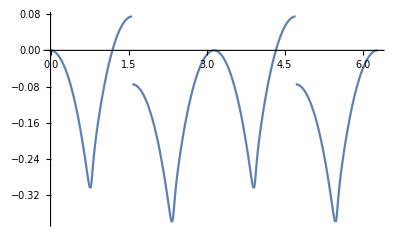

```mathematica
Plot[II2[t],{t,0,2Pi}]
```

```mathematica
dims=Table[0,{L}];
idx=1;
Monitor[
For[ϕ0=0,ϕ0<2Pi,ϕ0+=ρ,
(*K1=∫_0^ϕ0 (p[τ]-q[τ])ⅆτ;*)
K1=FunII2[ϕ0];
k1=Floor[-K1/(2Pi K)-1/(2 Pi K)Log[(2ϵ)/(CC(1-Exp[-2Pi K]))]];
rϕ[k_]:=CC Exp[-(2Pi K k+K1)];
AK=(rϕ[k1]^2)Pi/L;
Sumr=CC Exp[-K1] (1-Exp[-2Pi K(k1+1)])/(1-Exp[-2Pi K]);
AT=Sumr*ρ*2ϵ + (k1+1)ϵ^2;
d=2-Log[AK+AT]/Log[ϵ];
dims[[idx]]=N[d,20];
idx++;],
List[idx,N[ϕ0,20],N[K1,20],N[k1,20],N[d,20]]]
```

```mathematica
Print["Min dim = ",Min[dims],",  Max dim = ", Max[dims]]
```

Min dim = 0.9998557518099759239,  Max dim = 0.99988177830021279607

```mathematica
dth=1;
```

```mathematica
Print["Theory dim = ", dth, " (", N[dth],"), numerical dim = ", Max[dims]]
```

Theory dim = 1 (1.), numerical dim = 0.99988177830021279607